# Evaluate Momentum - Autocorrelation Function

## According to [J.Phys.A : Math. Theor. 42 (2009) 214048]

## Initial Data

```mathematica
SetDirectory["/home1/m.winkel/workspace/pepc.newstruct/examples/mw_cluster"]
filenameKt="momentum_electrons_Kt.dat"
filenameP="momentum_electrons.dat"
filenameCluster="cluster.dat"
filenameEnergy="energy.dat"
```

/home1/m.winkel/workspace/pepc.newstruct/examples/mw_cluster

momentum_electrons_Kt.dat

momentum_electrons.dat

cluster.dat

energy.dat

### import cluster data

```mathematica
ClusterImp=Import[filenameCluster]⟦2;;-1,All⟧;
```

#### Cluster Radius

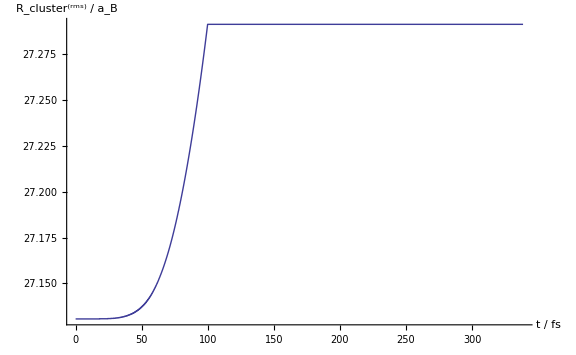

```mathematica
RadiusPlot=ListPlot[ClusterImp⟦All,{2,3}⟧,AxesLabel->{"t / fs","R_cluster^(rms) / a_B"},Joined->True, ImageSize->Large]
Export[filenameCluster<>"_Radius.pdf",RadiusPlot];
```

#### Cluster Ionization degree

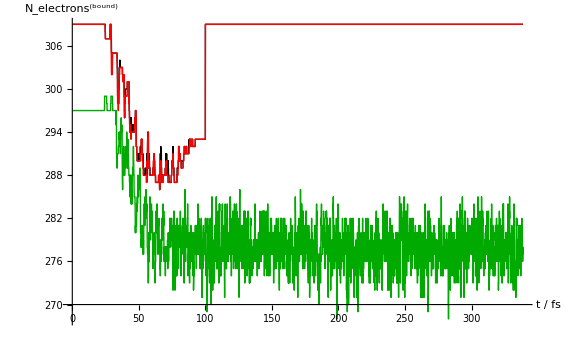

```mathematica
Needs["PlotLegends`"]
IonizationPlot=ListPlot[{ClusterImp⟦All,{2,6}⟧,ClusterImp⟦All,{2,7}⟧,ClusterImp⟦All,{2,8}⟧},AxesLabel->{"t / fs","N_electrons^(bound)"},Joined->True,PlotStyle->{Black,Darker[Green],Red},PlotRange->Full,PlotLegend->{"E_tot< 0 ∨ r < R_cluster^(rms)","r < R_cluster^(rms)","E_tot< 0"}, ImageSize->Large,LegendPosition->{1.05,0.0},LegendSize->{0.75,0.5}]
Export[filenameCluster<>"_Ionization.pdf",IonizationPlot];
```

### import energy data

```mathematica
EnergyImp=Import[filenameEnergy]⟦2;;-1,All⟧;
```

#### Eenrgy Plot

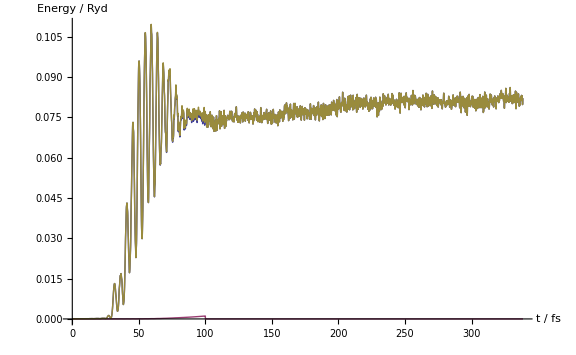

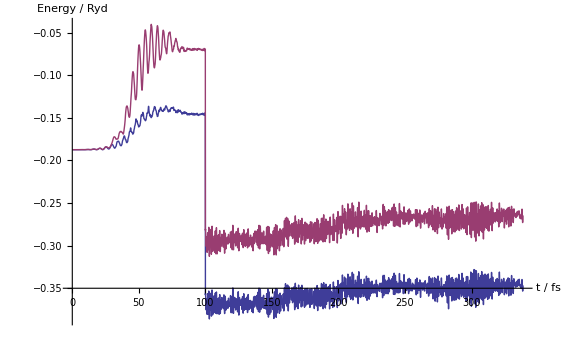

```mathematica
Needs["PlotLegends`"]
EnergyPlot1=ListPlot[{EnergyImp⟦All,{1,5}⟧,EnergyImp⟦All,{1,6}⟧,EnergyImp⟦All,{1,7}⟧},AxesLabel->{"t / fs","Energy / Ryd"},Joined->True,PlotRange->Full,PlotLegend->{"E_kin^(e)","E_kin^(i)","E_kin^(e + i)"}, ImageSize->Large,LegendPosition->{0.0,0.0},LegendSize->{0.3,0.3}]
Export[filenameEnergy<>"1.pdf",EnergyPlot1];
EnergyPlot2=ListPlot[{EnergyImp⟦All,{1,2}⟧,EnergyImp⟦All,{1,10}⟧},AxesLabel->{"t / fs","Energy / Ryd"},Joined->True,PlotRange->Full,PlotLegend->{"E_pot^(e + i)","E_tot"}, ImageSize->Large,LegendPosition->{0.0,0.0},LegendSize->{0.3,0.3}]
Export[filenameEnergy<>"2.pdf",EnergyPlot2];
```

### import momentum autocorrelation function

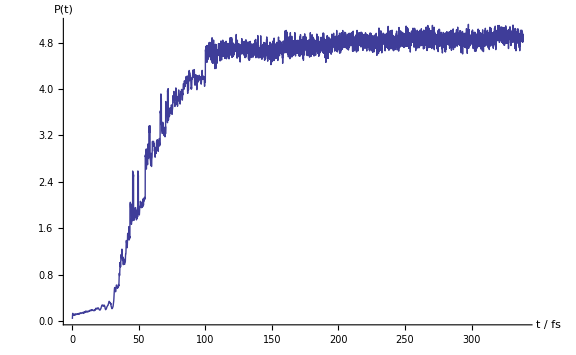

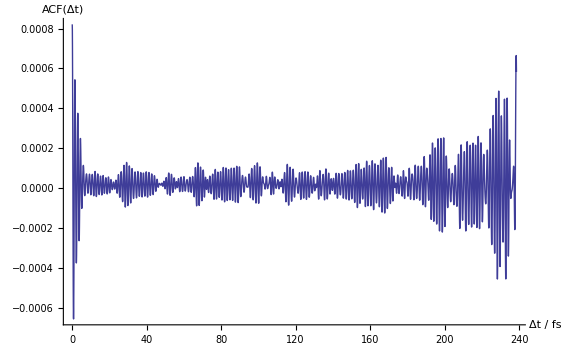

```mathematica
KtTblImp=Import[filenameKt][[;;]];
PTblImp=Import[filenameP][[All,{2,6}]];
PTblImpPlot=ListPlot[PTblImp,Joined->True,AxesLabel->{"t / fs",P["t"]},ImageSize->Large]
Export[filenameP<>".pdf",PTblImpPlot];
KtTblImpPlot=ListPlot[KtTblImp,Joined->True,AxesLabel->{"Δt / fs",ACF["Δt"]},ImageSize->Large]
Export[filenameKt<>".pdf",KtTblImpPlot];
```

### Number of Lines in raw data

```mathematica
Nges=Length[KtTblImp]
```

4009

### Timestep

```mathematica
Δt=KtTblImp[[2,1]]-KtTblImp[[1,1]]
```

0.0595325

## Fourier Transform

### Fourier transform of momentum autocorrelation function

```mathematica
a= 1; (* Fourier normalization coefficient: 1/n^((1-a)/2) *)
b= 1;(* Fourier exponent coefficient: e^(2π i b(r-1)(s-1)/n) *)
FC=Fourier[KtTblImp[[All,2]],FourierParameters->{a,b}];
ReFC=Re[FC];
ImFC=Im[FC];
PowerSpectrum=Abs[FC];
```

### appropriate frequency values

```mathematica
ωmax = 2π b/Δt
Δω=ωmax/Nges
ωlist=Table[N[Δω (i-1)],{i,1,Nges}];
```

105.542

0.0263263

### Identification of maximum

```mathematica
maxval=Max[PowerSpectrum]
pos = Position[PowerSpectrum, maxval][[1,1]]
maxfreq=ωlist[[pos]]
```

0.112537

155

4.05425

### Tables of Values

```mathematica
Nmax = Round[N[Nges/2]] (* Abttasttheorem ! *)
FCTable=Transpose[{ωlist,FC}[[All,1;;Nmax]]];
PowerSpectrumTable=Transpose[{ωlist,PowerSpectrum}[[All,1;;Nmax]]];
ReFCTable=Transpose[{ωlist,ReFC}[[All,1;;Nmax]]];ImFCTable=Transpose[{ωlist,ImFC}[[All,1;;Nmax]]];
```

2004

### Plot of spectrum and maximum

8.

2.

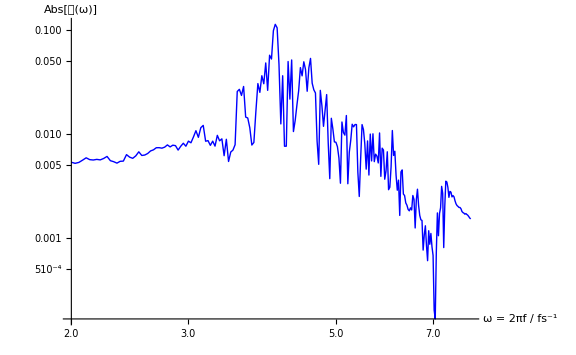

```mathematica
ωplotmax = 8.
ωplotmin=2.

plotmin=LengthWhile[ωlist,#<ωplotmin&]+1;
plotmax=LengthWhile[ωlist,#<ωplotmax&];

PowerSpectrumPlot=ListLogLogPlot[
{PowerSpectrumTable[[plotmin;;plotmax,All]],Transpose[{{maxfreq},{maxval}}]},
PlotStyle->{Blue,Red},AxesLabel->{"ω = 2πf / fs^-1",Abs[𝔉["ω"]]},PlotRange->Full,ImageSize->Large,Joined->True(*, PlotMarkers->Automatic*)]
Export[filenameKt<>".fourier_PowerSpectrum.pdf",PowerSpectrumPlot];
```

### Plot of Real Part of Fourier Coefficients

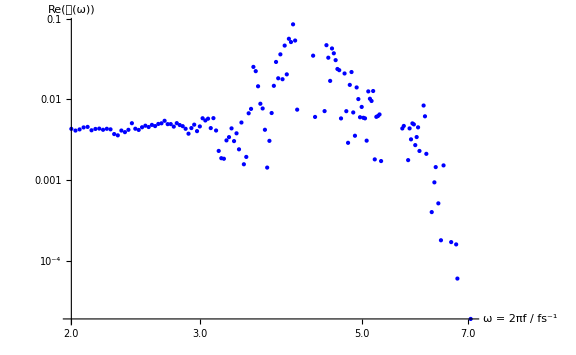

```mathematica
ReFCPlot=ListLogLogPlot[
ReFCTable[[plotmin;;plotmax,All]],
PlotStyle->Blue,AxesLabel->{"ω = 2πf / fs^-1",Re[𝔉["ω"]]},PlotRange->Full,ImageSize->Large,Joined->False(*, PlotMarkers->Automatic*)]
Export[filenameKt<>".fourier_ReFC.pdf",ReFCPlot];
```

### Plot of Imaginary Part of Fourier Coefficients

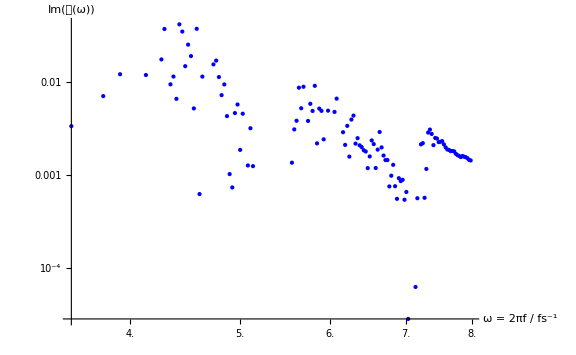

```mathematica
ImFCPlot=ListLogLogPlot[
ImFCTable[[plotmin;;plotmax,All]],
PlotStyle->Blue,AxesLabel->{"ω = 2πf / fs^-1",Im[𝔉["ω"]]},PlotRange->Full,ImageSize->Large,Joined->False(*, PlotMarkers->Automatic*)]
Export[filenameKt<>".fourier_ImFC.pdf",ImFCPlot];
```